This notebook shows how to calculate Doppler broadening for a time-modulated Rydberg sensor using the method outlined in the paper “Exact steady state of perturbed open quantum systems”: https://arxiv.org/abs/2501.06134 and the paper “Fast and Accurate Method for Doppler Averaging of Rydberg EIT Signals”: https://arxiv.org/abs/2501.02141. Screenshots haven been taken from the first paper to help with explaining the code better. Note that the notation in the two papers are different.  

This code generates Fig. 6 in the paper “Exact steady state of perturbed open quantum systems”.

If you use this work for research, we would appreciate citing the papers.

- Omar Nagib* and Thad G. Walker**

*onagib@wisc.edu
**tgwalker@wisc.edu

Install the packages MaTeX and CustomTicks to properly generate the figures:

```mathematica
<<MaTeX`
```

```mathematica
Get["CustomTicks`"]
```

************************************************************************************

Notational definitions

vectorization:  want to represent the N×N density matrix as a N^2 column vector

let v(A)=|A)=∑_ij A_ij i⊗j=∑_ij A_ij i j
Example:  two-level atom ρ=ρ_ee | ρ_eg
ρ_ge | ρ_gg->v(ρ)=ρ_ee
ρ_eg
ρ_ge
ρ_gg

```mathematica
<<Notation`
```

```mathematica
v[A_]:=Flatten[A]
```

Define ⊗ as Kronecker product of x and y:

```mathematica
ClearAll[CircleTimes];

CircleTimes[x_,y_]:=KroneckerProduct[x,y];
```

Define the symbol 𝕀_n as the n by n Identity matrix:

```mathematica
ClearAll[𝕀];
Subscript[𝕀,n_]:=IdentityMatrix[n];
```

Define ᵀ as transpose:

```mathematica
Notation[ParsedBoxWrapper[SuperscriptBox[x_,"ᵀ"]]⟹ParsedBoxWrapper[RowBox[{"Transpose","[",x,"]"}]]];
```

Define † as conjugate transpose:

```mathematica
Notation[ParsedBoxWrapper[SuperscriptBox[x_,"†"]]⟹ParsedBoxWrapper[RowBox[{"ConjugateTranspose","[",x,"]"}]]];
```

Define | ⟩ as a column vector, a ket:

```mathematica
ClearAll[Ket];

Ket[v_List]:=Transpose[{Flatten[v]}];
```

Define * as conjugate transpose:

```mathematica
Notation[ParsedBoxWrapper[SuperscriptBox[x_,"*"]]⟹ParsedBoxWrapper[RowBox[{"Conjugate","[",x,"]"}]]];
```

************************************************************************************
The Floquet approach:

-Graphics-

-Graphics-
-Graphics-

Here we carry out the Floquet analysis for the four-level ladder system.

Let’s study a system with four energy levels: s, p, d, and f.

```mathematica
s={0,0,0,1};p={0,0,1,0};d={0,1,0,0};f={1,0,0,0};
```

Construct the Hamiltonian part without the time modulation [i.e., without ϵ_2(t)]:

```mathematica
H=-Δ p⊗pᵀ-δ d⊗dᵀ-δ f⊗fᵀ+Subscript[ϵ, 1]/2(s⊗Transpose[p]+p⊗Transpose[s])+Subscript[ϵ, 3]/2(f⊗Transpose[d]+d⊗Transpose[f])
```

{{-δ,ϵ_3/2,0,0},{ϵ_3/2,-δ,0,0},{0,0,-Δ,ϵ_1/2},{0,0,ϵ_1/2,0}}

The Lindblad operator:

```mathematica
L=Sqrt[Γ]s⊗Transpose[p];
```

Construct the corresponding Lindbladian:

```mathematica
ℒ=-I(H⊗Subscript[𝕀, Length[H]]-Subscript[𝕀, Length[H]]⊗Hᵀ)+( L⊗L-1/2 Lᵀ.L⊗Subscript[𝕀, Length[H]]-1/2 Subscript[𝕀, Length[H]]⊗Lᵀ.L);
```

Construct the time-modulated part of the Hamiltonian and the corresponding Lindbladian:

```mathematica
Hmod=Subscript[ϵ, 2]/2(p⊗Transpose[d]+d⊗Transpose[p])
```

{{0,0,0,0},{0,0,ϵ_2/2,0},{0,ϵ_2/2,0,0},{0,0,0,0}}

```mathematica
ℒmod=-I(Hmod⊗Subscript[𝕀, Length[H]]-Subscript[𝕀, Length[H]]⊗Hmodᵀ);
```

Define the trace function for four energy levels:

```mathematica
vecI=v[Subscript[𝕀, 4]];
```

```mathematica
vecIdag=SuperDagger[v[Subscript[𝕀, 4]]];
```

```mathematica
tr4[A_]:=vecIdag.A
```

Construct the Floquet matrix with 9 harmonics (-4 f_0 to 4 f_0), with ℒ-n i f_0 along the diagonal and ℒ_mod/2 along the off-diagonal (cf. the paper for explanation). ℒ and ℒ_mod are 16 by 16 matrices and ρ_F=(ρ_N,...,ρ_-N)^T:

```mathematica
ℒfloqfour=ArrayFlatten[Table[(ℒ-(5-i) f0 I IdentityMatrix[16]) KroneckerDelta[i,j]+1/2 ℒmod KroneckerDelta[i+1,j]+1/2 ℒmod KroneckerDelta[i-1,j] ,{i,1,9},{j,1,9}]];
```

```mathematica
pFour={4,3,2,1,0,-1,-2,-3,-4};
```

```mathematica
vsp=SuperDagger[v[s⊗p]];
```

```mathematica
vps=SuperDagger[v[p⊗s]];
```

Initialize parameter values:

```mathematica
k1=1/(.78);(*in micrometer, D2 780 nm transition*)
```

```mathematica
k2=(1/(.78)-1/(.48)); (*two photon transition from ground state to Rydberg*)
```

```mathematica
ℒ0=ℒfloqfour/.{Subscript[ϵ, 2]->1.,f0-> 1.,Subscript[ϵ, 1]->2.,Subscript[ϵ, 3]->1.,Γ->6.,Δ->0.,δ->0.};
```

```mathematica
ℒδ=D[ℒfloqfour,δ];
```

************************************************************************************
Doppler averaging by numerical sampling and Riemann sum

-Graphics-

Here, we sample uniformly sample over the Maxwell-Boltzmann distribution to find the steady state at many velocities, and we compute the Doppler average using a Riemann sum. the Let’s introduce velocity dependence:

```mathematica
vt=169.474; (*thermal velocity*)
```

```mathematica
w[v_,vt_]=1/(Sqrt[2 Pi]vt)Exp[-v^2/(2vt^2)];
```

Let’s create a Module implementation of the code that produces the list of the normalized output { ρ_m(v)}:

The inputs are (velocity, modulation amplitude ϵ2 AKA ϵ0, modulation frequency f, ϵ1, ϵ3, Γ, Δ, δ):

Construct  ℒ_1, where ℒ_1 is the Doppler shifted part of the Floquet matrix, computed by ℒ_1=(dℒ_0(Δ-k_1 v,δ-k_2 v))/dv.

```mathematica
ℒ1=D[ℒfloqfour/.{Δ->Delta-k1 v,δ->delta-k2 v},v];
```

```mathematica
ρv[vel_,delta_]:=Block[{delta0=delta,vel0=vel,Gfloq4v0,ρFtest4v0,ρtest4v0},(*define Doppler shifted Floquet matrix*)Gfloq4v0=ℒ0+delta0 ℒδ+vel0 ℒ1;(*Find the nullspace vector, i.e., steady state solution*)
ρFtest4v0=Flatten[Eigenvectors[Gfloq4v0,1,Method->{"Arnoldi","Shift"->0}]];
(*flatten the solution, so we have a really long Floquet vector [ρN,ρ(N-1),...,ρ-N], here for N=4, we have 9 harmonics, and each of these ρN is length 16 because this is a vectorized four level system*)
ρtest4v0=Partition[ρFtest4v0,16];(*divided the Floquet vector into a list  { Subscript[ρ, m](v)}*)
ρtest4v0=ρtest4v0/tr4[ρtest4v0[[5]]](*normalize solution by ρ0, Note the norm of other harmonics is zero, which can be proved*)
]
```

Using the { ρ_m(v)} output from the module above, average it over a Gaussian by a Riemann sum:

Now compute complete time dependence ρ_v(t) for a given v:

```mathematica
ρvt[vel_,delta_,t_]:=Module[{delta0=delta,rhotemp,rhooutput,vel0=vel},rhotemp=ρv[vel0,delta0];rhooutput=Sum[rhotemp[[i]] ⅇ^(ⅈ pFour⟦i⟧ 2π 1. t) ,{i,1,9}]]
```

Approach 1: do a unifrom Riemann Sum over the set  { ρ_m(v)} to obtain  { ρ_m(avg)} from -3 v_th to 3 v_th, and specify the number of samples P+1 with spacing dv=(6vt)/P:

```mathematica
ρDopplerP[delta_,P_]:=Module[{P0=P,dv},(*equal spacing of dv over the entire range 6vt*)dv=6 vt/P0;Sum[ρv[vel,delta]w[vel,vt]dv,{vel,-3vt,3vt,dv}]]
```

```mathematica
ρDopplerPt[delta_,P_,t_]:=Module[{delta0=delta,rhotemp,rhooutput,P0=P},rhotemp=ρDopplerP[delta0,P0];rhooutput=Sum[rhotemp[[i]] ⅇ^(ⅈ pFour⟦i⟧ 2π 1. t) ,{i,1,9}]]
```

Approach 2: Do an efficient inverse-transform sampling as described in “Inverse Transform Sampling for Efficient Doppler-Averaged Spectroscopy Simulations”, see https://arxiv.org/pdf/2304.12468.

```mathematica
(*Inverse-transform Doppler average*)
ρDopplerInvSampleP[δ_,P_Integer?Positive]:=Module[{η,vSamples},(*1) build P equally-populated quantiles η_j=(2j–1)/P–1,j=1…P*)η=Table[-1.+(2. i-1.)/P,{i,1.,P}];
(*2) map through InverseErf per Eq.(7):v_j=vσ√2·InverseErf[η_j]*)vSamples=vt √2. InverseErf[η];
(*3) average your steady-states at those speeds*)Mean[ρv[#,δ]&/@vSamples]];
```

```mathematica
ρDopplerInvSamplePt[delta_,P_,t_]:=Module[{delta0=delta,rhotemp,rhooutput,P0=P},rhotemp=ρDopplerInvSampleP[delta0,P0];rhooutput=Sum[rhotemp[[i]] ⅇ^(ⅈ pFour⟦i⟧ 2π 1. t) ,{i,1,9}]]
```

************************************************************************************
Constructing the Drazin inverse (using three different methods):

Method 1 (diagonalization):

Important note: 
In the paper, the way the generalized inverse is constructed as follows:

ℒ_0^-=(1/(G_-)R_- ).(L_-)^T (normal version)
-Graphics-

However, Mathematica Eigensystem’s system returns the eigenvectors as rows not columns. Therefore, in the Mathematica implementation we have
ℒ_0^-=(1/(G_-)R_- )^T.L_-   (Mathematica version)

Let’s show this this works for an example:

```mathematica
ℒTest=ℒfloqfour/.{Subscript[ϵ, 2]->1.,f0-> 1.,Subscript[ϵ, 1]->1.,Subscript[ϵ, 3]->1.,Γ->1.,Δ->1.,δ->1.};
(*find solution to the zero velocity problem*)
ρ0Test=Flatten[NullSpace[ℒTest]];

ρ0Temp=Partition[ρ0Test,16];(*reshape and output the list {Subscript[ρ, m]}*)
Normρ0Test=tr4[ρ0Temp[[5]]];(*Compute the norm, note that only Subscript[ρ, 0] has non-zero norm, which is the 5th element in {Subscript[ρ, m]}*)
ρ0Test=ρ0Test/Normρ0Test;(*Normalize by the trace/norm*)

(*compute the Drazin inverse by diagonalization method*)
{gTest,RgTest}=Eigensystem[ℒTest];
LgTest=Inverse[Transpose[RgTest]];
ℒDrazinDiag=Transpose[(1/gTest[[1;;-2]])RgTest[[1;;-2,All]]].LgTest[[1;;-2,All]];
```

Method 2 (Using an inverse identity):
We note that ℒ_0^- can be directly constructed as

ℒ_0^-=(ℒ_0+ (R_0 L_0^T))^-1-R_0 L_0^T

i.e., add the nullspace projector P_0=R_0 L_0^T, take the inverse, and then subtract P_0 again. This completely avoids explicit diagonalization and construction of right/left eigenvectors. Since we are working in the expanded Floquet space here, we note that the leftnullspace eigenvector L_0^T= (vec(I_sys))^T⊗<e_0|, where vec(I_sys) is the vectorization of the identity matrix (denoted as vecI in the code) of the original system, and <e_0| is the unit vector that projects the Floquet Lindbladian into the zero-frequency harmonic component, i.e., project ρ(t)=∑_m ρ_m e^(-i m ω t) into ρ_(m=0).

```mathematica
(*2) pick out the zero-harmonic block (block i=5 of 1...9)*)
e0=UnitVector[9,5];                     (*length 9*)

(*Full Floquet left nullspace vector in Liouville space*)
vecIFloq=Flatten[KroneckerProduct[e0,vecI]];  

(*Check explicitly that this is the left nullspace vector of the Floquet Lindbladian*)
Transpose[vecIFloq].ℒTest
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
(*compute the Drazin inverse using the inversion method*)
P0=KroneckerProduct[ρ0Test,Transpose[vecIFloq]];
ℒDrazinInv=Inverse[ℒTest+P0]-P0;
```

Method 3 (Mathematica’s native Drazin Inverse function):

```mathematica
(*Compute the Drazin inverse usin Mathematica's native function*)
ℒDrazinMath=DrazinInverse[ℒTest];
```

Now compare the three approaches:

```mathematica
Max[Abs[ℒDrazinDiag-ℒDrazinInv]]
Max[Abs[ℒDrazinInv-ℒDrazinMath]]
Max[Abs[ℒDrazinDiag-ℒDrazinMath]]
```

4.90765×10^-13

1.41066×10^-13

5.11496×10^-13

```mathematica
Mean[Flatten[Abs[ℒDrazinDiag-ℒDrazinInv]]]
Mean[Flatten[Abs[ℒDrazinInv-ℒDrazinMath]]]
Mean[Flatten[Abs[ℒDrazinDiag-ℒDrazinMath]]]
```

1.73728×10^-15

1.03769×10^-15

2.15684×10^-15

Which shows numerical agreement between the three different approaches.

************************************************************************************
Doppler averaging using the present method

Here, we apply the present approach to do efficient Doppler averaging without any sampling of the Maxwell-Boltzmann distribution. Consult the paper on details of the theory and numerical implementation of the technique. 

The atomic state averaged over a Gaussian distribution (Doppler averaged atomic state) is given by
-Graphics-

where σ_v=v_th is the Maxwell-Boltzmann distribution’s width, i.e., the thermal velocity.  r_λ, l_λ and λ are the right, left eigenvectors and eigenvalues of the matrix ℒ_0^-ℒ_1. Here, ℒ_0 corresponds to the Floquet matrix at zero velocity, which has been constructed above. ℒ_0^- is the Drazin inverse of ℒ_0. We described above, how to construct this Drazin inverse efficiently. ℒ_1 is the Doppler shifted part of the Floquet matrix, computed by ℒ_1=(dℒ_0(Δ-k_1 v,δ-k_2 v))/dv.

Next, we define the function fdopplerArray which helps to efficiently compute the sum  via matrix multiplication and vectorized operations acting on a list.

```mathematica
(*Set the function to be Listable so it automatically maps over arrays*)SetAttributes[fdopplerArray,Listable];

(*Define the function for elements with magnitude less than 10^-3; ideally the function should give 1 only when the mangitude is zero; the 10^-3 cutoff can be changed as appropriate*)
fdopplerArray[λ_/;Abs[λ]<10^-3]:=1;
fdopplerArray[Λ_]:=(ⅇ^(-1/(2 Λ^2 vt^2)) √(π/2) (1+Erf[(√(-Λ^2))/(√2 Λ^2 vt)]))/(√(-Λ^2) vt);
```

Let’s denote r=(r_1 r_2...r_N) as the matrix made from the right eigenvectors of ℒ_0^-.ℒ_1 and l=(l_1 l_2...l_N) are the left eigenvectors and Λ=(λ_1 λ_2... λ_N) are the eigenvalues.

 The averaged atomic state can be efficiently constructed as:

(ρ_avg= (fdopplerArray[Λ]r])^T.l).ρ_0 (Mathematica’s version)

where ρ_0 is the solution at zero velocity. Note that ((fdopplerArray[Λ]r])^T.l) has this structure because the eigenvectors are listed in the rows not columns in Mathematica. In other languages, such as MATLAB, it would be given by

 ρ_avg= (fdopplerArray[Λ]r].l^T).ρ_0 (Non-Mathematica version)

Below  is a module that generates the Doppler averaged atomic state ρ_avg(t) using the present method:

```mathematica
ρavgt[delta_,t_]:=Block[{delta0=delta,t0=t,Gfloq4,ρv0,ρtest40,Normρv0,EigensystemGfloq4,Gfloq4v0inv,ρFloq4vavg,RhoDopplerfloq,λ,rλ,lλ,i,P0},(*numerically construct the Floquet matrix*)Gfloq4=ℒ0+delta0 ℒδ;
(*find solution to the zero velocity problem*)
ρv0=Flatten[Eigenvectors[Gfloq4,1,Method->{"Arnoldi","Shift"->0}]];
ρtest40=Partition[ρv0,16];(*reshape and output the list {Subscript[ρ, m]}*)
Normρv0=tr4[ρtest40[[5]]];(*Compute the norm, note that only Subscript[ρ, 0] has non-zero norm, which is the 5th element in {Subscript[ρ, m]}*)
ρv0=ρv0/Normρv0;(*Normalize by the trace/norm*)
(*compute the Drazin inverse using the inversion method*)
P0=KroneckerProduct[ρv0,Transpose[vecIFloq]];
Gfloq4v0inv=Inverse[Gfloq4+P0]-P0;
{λ,rλ}=Eigensystem[Gfloq4v0inv.ℒ1];(*Now diagonalize Subscript[ℒ, 0]^-Subscript[ℒ, 1] to find the right eigenvectors and eigenvalues*)
lλ=PseudoInverse[Transpose[rλ]];(*construct the left eigenvectors from the right eigenvectors*)
RhoDopplerfloq=Transpose[ fdopplerArray[λ]rλ].(lλ.ρv0);ρFloq4vavg=Module[{q=Partition[RhoDopplerfloq,16]},Sum[q⟦i⟧ⅇ^(ⅈ pFour⟦i⟧ 2π 1. t0) ,{i,9}]](*Construct the Doppler averaged atomic state Subscript[ρ, avg](t)*)]
```

************************************************************************************
Doppler averaging using the present method: Example

```mathematica
(*Generate the values for v from 0 to vt*)
vValues2=Table[v,{v,0,vt,1}];

(*Generate the colors from the TemperatureMap color scheme, with v=0 being deep blue and Subscript[v, th] being red*)
colors=Table[ColorData["TemperatureMap"][(1-Exp[-0.1i])],{i,0,vValues2[[Length[vValues2]]]}];
(*Generate the plot expressions for each v value*)
plotExpressions2=Table[Im[v[s⊗p]†.ρvt[vel,0,x]],{vel,vValues2}];
```

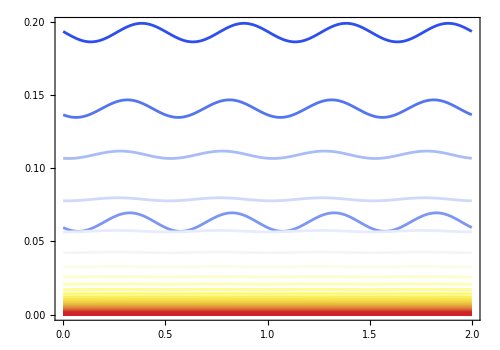

```mathematica
rhospvplot2=Plot[{plotExpressions2},{x,0,2},FrameLabel->{MaTeX["\\textsf{\\text{time}} \\mathsf{\\rm{(\\mu s)}}",Magnification->3],MaTeX["\\textsf{\\text{Im}}\\mathsf{(\\rho_{sp}) }",Magnification->3]},Frame->True,FrameStyle->Directive[GrayLevel[0],30,FontFamily->"Helvetica",AbsoluteThickness[1.0]],FrameTicks->{{LinTicks,False},{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&}},GridLines->None,PlotRange->All,Axes->False,ImageSize->500,AspectRatio->0.7,PlotStyle->colors]
```

Using the present approach, plot the Doppler averaged signal, without any sampling:

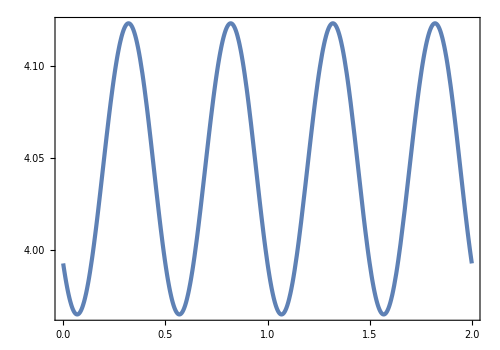

```mathematica
rhospavgplot=Plot[{Evaluate[10^3 Im[SuperDagger[v[s⊗p]].ρavgt[0,x]]]},{x,0,2},FrameLabel->{MaTeX["\\textsf{\\text{time}} \\mathsf{\\rm{(\\mu s)}}",Magnification->3],MaTeX["\\textsf{\\text{Im}}\\mathsf{(\\bar{\\rho}_{sp}) \\ (\\textsf{\\scriptsize \\(\\times 10^{-3}\\)})}",Magnification->3]},Frame->True,FrameStyle->Directive[GrayLevel[0],30,FontFamily->"Helvetica",AbsoluteThickness[1.0]],FrameTicks->{{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&},{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&}},GridLines->None,PlotRange->All,Axes->False,ImageSize->500,AspectRatio->0.7,PlotStyle->AbsoluteThickness[3]]
```

************************************************************************************
Present method vs sampling: Speed comparison

Create (P,CPU) list for the sampling approach:

```mathematica
PTime=Table[{P,First@Timing[vps.ρDopplerPt[1.,P,t];]},{P,{10,100,1000,10000}}];
```

```mathematica
PTime
```

{{10,0.121505},{100,1.01635},{1000,10.1311},{10000,102.858}}

Time for inverse transform sampling approach:

```mathematica
PInvTime=Table[{P,First@Timing[vps.ρDopplerInvSamplePt[1.,P,t];]},{P,{10,100,1000,10000}}];
```

```mathematica
PInvTime
```

{{10,0.114913},{100,1.01779},{1000,10.4217},{10000,103.442}}

CPU time using the present approach:

```mathematica
PresentTime=First@Timing[vps.ρavgt[1.,t]];
```

```mathematica
PresentTime
```

0.076643

```mathematica
PTimepresent=Table[{P,PresentTime},{P,{10,100,1000,10000}}];
```

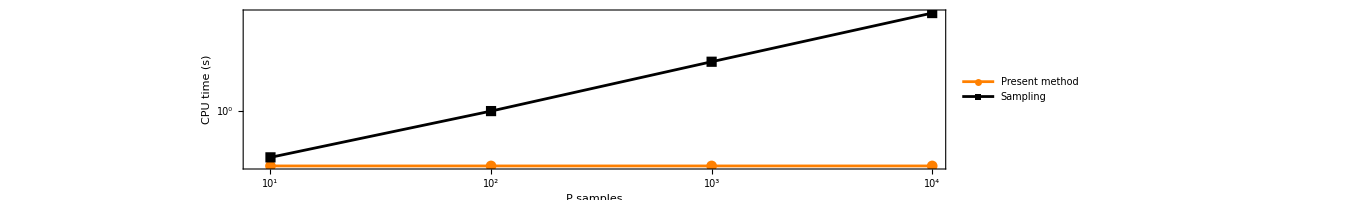

```mathematica
CPUTimePlot=ListPlot[{Log10[PTimepresent],Log10[PInvTime]},FrameLabel->{"P samples","CPU time (s)"},Frame->True,FrameStyle->Directive[GrayLevel[0],30,FontFamily->"Times New Roman",AbsoluteThickness[1.0]],GridLines->None,PlotRange->All,FrameTicks->{{LogTicks[-6,4,TickLabelStep->1],None},{LogTicks[0,5,TickLabelStep->1],LinTicks[#1,#2,ShowTickLabels->False]&}},Axes->False,PlotStyle->{Directive[Orange,AbsolutePointSize[8]],Directive[Black,AbsolutePointSize[5],Style["■"]]},LabelStyle->{FontSize->25,FontFamily->"Times New Roman"},PlotLegends->Placed[LineLegend[{"Present method","Sampling"},LegendMarkerSize->{30,10}],{0.2,0.7}],Axes->False,Joined->True,PlotMarkers->Automatic,AspectRatio->0.2,ImageSize->1000]
```

***************************************************************************************************************************

The figures below are the peak-to-peak amplitude of the signal Im(ρ_sp(t)) before and after Doppler averaging. Doppler averaging is done using the present method.

peak-to-peak amplitude of the signal Im(ρ_sp(t)) at v=0:

```mathematica
DeltaAmpχ=Table[{δ,10^3(FindMaximum[{Im[vsp.ρvt[0.,δ,t]],t>=0},{t,1}][[1]]-FindMinimum[{Im[vsp.ρvt[0.,δ,t]],t>=0},{t,1}][[1]])},{δ,-10.,10.,0.1}];
```

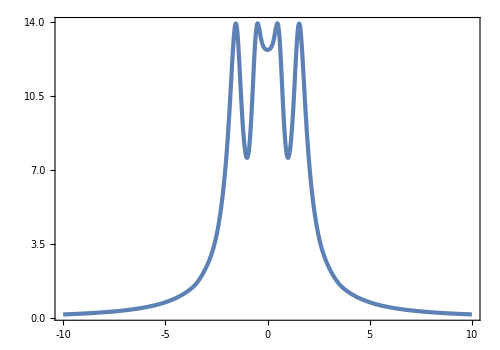

```mathematica
DeltaAmpχPlot=ListPlot[{DeltaAmpχ},Joined->True,InterpolationOrder->2,PlotRange->All,PlotStyle->{AbsoluteThickness[3]},FrameLabel->{MaTeX["\\delta/2\\pi \ (\\text{MHz})",Magnification->3],MaTeX["\\text{\\text{Im}}(\\rho_{\\rm sp}) \\ (\\text{\\scriptsize \\(\\times 10^{-3}\\)})",Magnification->3]},Frame->True,FrameStyle->Directive[GrayLevel[0],30,FontFamily->"Times New Roman",AbsoluteThickness[1.0]],FrameTicks->{{LinTicks[0,14,3.5,5,TickLabelStep->1],LinTicks[#1,#2,ShowTickLabels->False]&},{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&}},GridLines->None,ImageSize->500,PlotRange->All,Axes->False,PlotStyle->{Directive[Orange,AbsoluteThickness[3]],Directive[Gray,DotDashed,AbsoluteThickness[10]]},LabelStyle->{FontSize->22,FontFamily->"Times New Roman"},AspectRatio->0.7,PlotLegends->Placed[LineLegend[{"","",""},LegendMarkerSize->{0.1,0.1}],{0.8,0.7}]]
```

Doppler  averaged signal using the exact method:

```mathematica
(*DeltaAmpavgχ=Table[{δ,10^3(FindMaximum[{Im[vsp.ρavgt[δ,t]]},{t}][[1]]-FindMinimum[{Im[vsp.ρavgt[δ,t]]},{t}][[1]])},{δ,-10.,10.,0.1}];*)
```

```mathematica
DeltaAmpavgExact=Table[Module[{fexpr,tmin=0,tmax=2,p2p},(*define the real-valued function of t*)fexpr=Im[vps.ρavgt[δ,t]];
(*global max& min on 0≤t≤2*)p2p=NMaxValue[{fexpr,tmin<=t<=tmax},t]-NMinValue[{fexpr,tmin<=t<=tmax},t];
{δ,10^3 p2p}],{δ,-10.,10.,0.1}];
```

Doppler  averaged signal by sampling P_v=101 points

```mathematica
(*DeltaAmpavgχSample100=Table[{δ,10^3(FindMaximum[Im[vsp.ρDopplerPt[δ,100,t]],t][[1]]-FindMinimum[Im[vsp.ρDopplerPt[δ,100,t]],t][[1]])},{δ,-10.,10.,0.1}];*)
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

Uniform sampling:

```mathematica
DeltaAmpavgChiSample100=Table[Module[{fexpr,tmin=0,tmax=2,p2p},(*define the real-valued function of t*)fexpr=Im[vps.ρDopplerPt[δ,100,t]];
(*global max& min on 0≤t≤2*)p2p=NMaxValue[{fexpr,tmin<=t<=tmax},t]-NMinValue[{fexpr,tmin<=t<=tmax},t];
{δ,10^3 p2p}],{δ,-10.,10.,0.1}];
```

Inverse transform sampling:

```mathematica
DeltaAmpavgChiInvSample100=Table[Module[{fexpr,tmin=0,tmax=2,p2p},(*define the real-valued function of t*)fexpr=Im[vps.ρDopplerInvSamplePt[δ,101,t]];
(*global max& min on 0≤t≤2*)p2p=NMaxValue[{fexpr,tmin<=t<=tmax},t]-NMinValue[{fexpr,tmin<=t<=tmax},t];
{δ,10^3 p2p}],{δ,-10.,10.,0.1}];
```

P_v=501 uniform sampling:

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
DeltaAmpavgChiSample500=Table[Module[{fexpr,tmin=0,tmax=2,p2p},(*define the real-valued function of t*)fexpr=Im[vps.ρDopplerPt[δ,500,t]];
(*global max& min on 0≤t≤2*)p2p=NMaxValue[{fexpr,tmin<=t<=tmax},t]-NMinValue[{fexpr,tmin<=t<=tmax},t];
{δ,10^3 p2p}],{δ,-10.,10.,0.1}];
```

P_v=1001 uniform sampling

NMinValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
DeltaAmpavgChiSample1000=Table[Module[{fexpr,tmin=0,tmax=2,p2p},(*define the real-valued function of t*)fexpr=Im[vps.ρDopplerPt[δ,1000,t]];
(*global max& min on 0≤t≤2*)p2p=NMaxValue[{fexpr,tmin<=t<=tmax},t]-NMinValue[{fexpr,tmin<=t<=tmax},t];
{δ,10^3 p2p}],{δ,-10.,10.,0.1}];
```

NMinValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

P_v=1001 inverse transform sampling

```mathematica
DeltaAmpavgChiInvSample1000=Table[Module[{fexpr,tmin=0,tmax=2,p2p},(*define the real-valued function of t*)fexpr=Im[vps.ρDopplerInvSamplePt[δ,1001,t]];
(*global max& min on 0≤t≤2*)p2p=NMaxValue[{fexpr,tmin<=t<=tmax},t]-NMinValue[{fexpr,tmin<=t<=tmax},t];
{δ,10^3 p2p}],{δ,-10.,10.,0.1}];
```

Plot  uniform sampling result and compare it with the present method

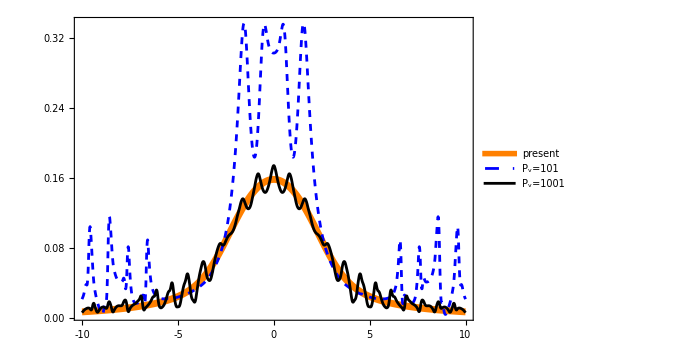

```mathematica
DeltaAmpχavgPlot=ListPlot[{DeltaAmpavgExact,DeltaAmpavgChiSample100,DeltaAmpavgChiSample1000},Joined->True,InterpolationOrder->2,PlotRange->All,FrameLabel->{MaTeX["\\delta/2\\pi \ (\\text{MHz})",Magnification->3],MaTeX["\\text{\\text{Im}}(\\bar{\\rho}_{\\rm sp}) \\ (\\text{\\scriptsize \\(\\times 10^{-3}\\)})",Magnification->3]},Frame->True,FrameStyle->Directive[GrayLevel[0],30,FontFamily->"Times New Roman",AbsoluteThickness[1.0]],FrameTicks->{{LinTicks[0,0.37,0.08,5,TickLabelStep->1],LinTicks[#1,#2,ShowTickLabels->False]&},{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&}},GridLines->None,ImageSize->500,PlotRange->All,Axes->False,LabelStyle->{FontSize->18,FontFamily->"Times New Roman"},AspectRatio->0.7,PlotLegends->Placed[LineLegend[{"present","P_v=101","P_v=1001"},LegendMarkerSize->{40,20}],{0.8,0.7}],PlotStyle->{Directive[Orange,AbsoluteThickness[5]],Directive[Blue,Dashed,AbsoluteThickness[2]],Directive[Black,AbsoluteThickness[2]]}]
```

Plot  inverse tranform sampling result and compare it with the present method

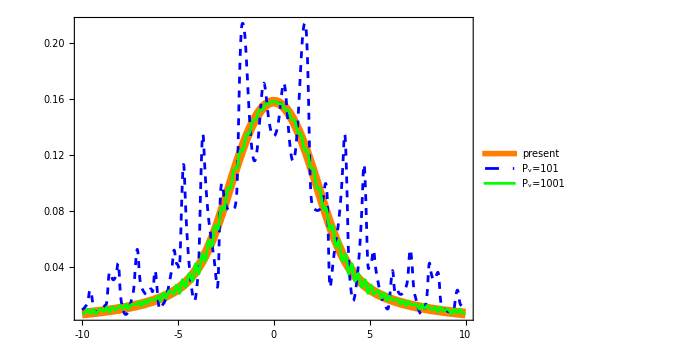

```mathematica
DeltaAmpχavgInvPlot=ListPlot[{DeltaAmpavgExact,DeltaAmpavgChiInvSample100,DeltaAmpavgChiInvSample1000},Joined->True,InterpolationOrder->2,PlotRange->All,FrameLabel->{MaTeX["\\delta/2\\pi \ (\\text{MHz})",Magnification->3],MaTeX["\\text{\\text{Im}}(\\bar{\\rho}_{\\rm sp}) \\ (\\text{\\scriptsize \\(\\times 10^{-3}\\)})",Magnification->3]},Frame->True,FrameStyle->Directive[GrayLevel[0],30,FontFamily->"Times New Roman",AbsoluteThickness[1.0]],FrameTicks->{{LinTicks[0.,0.3,0.04,5,TickLabelStep->1],LinTicks[#1,#2,ShowTickLabels->False]&},{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&}},GridLines->None,ImageSize->500,PlotRange->All,Axes->False,LabelStyle->{FontSize->18,FontFamily->"Times New Roman"},AspectRatio->0.7,PlotLegends->Placed[LineLegend[{"present","P_v=101","P_v=1001"},LegendMarkerSize->{40,20}],{0.8,0.75}],PlotStyle->{Directive[Orange,AbsoluteThickness[7]],Directive[Blue,Dashed,AbsoluteThickness[2]],Directive[Green,AbsoluteThickness[2]]}]
```

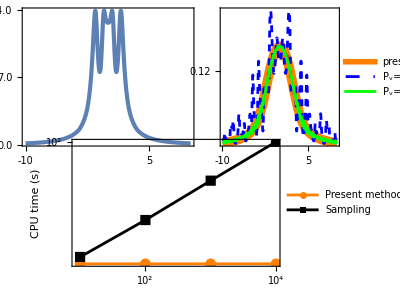

```mathematica
GraphicsGrid[{{DeltaAmpχPlot,DeltaAmpχavgInvPlot},{CPUTimePlot,SpanFromLeft}},ImageSize->Full,Alignment->Center,Spacings->{-10,-70}]
```